```mathematica
f[y_]:=(1-Exp[-2n(g2-y)(g1-x)])PDF[NormalDistribution[0,1/(√n)],y-x]If[y<g2,1,0]
```

```mathematica
Assuming[n>0 &&g1>0 &&g2>0 && Element[g1, Reals] && Element[g2, Reals]&& Element[x, Reals]&& Element[y, Reals] && Element[n, Reals],FourierTransform[f[t],t,s,FourierParameters->{0,-2Pi}]]
```

```mathematica
fhat[s_]:=(ⅇ^(-(2 π s (π s+ⅈ n x))/n-2 g1 (g2 n+2 ⅈ π s+n x)) √n (ⅇ^(2 g1 (g2 n+2 ⅈ π s+n x)) (g2 n+2 ⅈ π s-n x) √((-2 g1 n+g2 n+2 ⅈ π s+n x)^2) Erf[(√((g2 n+2 ⅈ π s-n x)^2/n))/(√2)]+√((g2 n+2 ⅈ π s-n x)^2) ((ⅇ^(2 g1 (g2 n+2 ⅈ π s+n x))-ⅇ^(2 g1^2 n+2 g2 n x+4 ⅈ π s x)) √((-2 g1 n+g2 n+2 ⅈ π s+n x)^2)+ⅇ^(2 g1^2 n+2 g2 n x+4 ⅈ π s x) (2 g1 n-g2 n-2 ⅈ π s-n x) Erf[(√((-2 g1 n+g2 n+2 ⅈ π s+n x)^2/n))/(√2)])))/(2 √(n (g2 n+2 ⅈ π s-n x)^2) √((-2 g1 n+g2 n+2 ⅈ π s+n x)^2))
```

```mathematica
fhat[s]/.(g2 n+2 ⅈ π s+n x)-> a
```

1/(2 √((a-2 g1 n)^2) √(n (g2 n+2 ⅈ π s-n x)^2))ⅇ^(-2 a g1-(2 π s (π s+ⅈ n x))/n) √n (√((g2 n+2 ⅈ π s-n x)^2) ((ⅇ^(2 a g1)-ⅇ^(2 g1^2 n+2 g2 n x+4 ⅈ π s x)) √((a-2 g1 n)^2)+ⅇ^(2 g1^2 n+2 g2 n x+4 ⅈ π s x) (2 g1 n-g2 n-2 ⅈ π s-n x) Erf[(√((a-2 g1 n)^2/n))/(√2)])+ⅇ^(2 a g1) √((a-2 g1 n)^2) (g2 n+2 ⅈ π s-n x) Erf[(√((g2 n+2 ⅈ π s-n x)^2/n))/(√2)])

```mathematica
FullSimplify[fhat[s],n>0 &&g1>0 &&g2>0 && Element[g1, Reals] && Element[g2, Reals]&& Element[x, Reals]&& Element[s, Reals] && Element[n, Reals]]
```

1/2 ⅇ^(-(2 π s (π s+ⅈ n x))/n) (1+Erf[(g2 n+2 ⅈ π s-n x)/(√2 √n)]+ⅇ^(2 (g1 n-g2 n-2 ⅈ π s) (g1-x)) (-2+Erfc[(2 ⅈ π s+n (-2 g1+g2+x))/(√2 √n)]))

```mathematica
fhatsimp[s_]:=1/2 ⅇ^(-(2 π s (π s+ⅈ n x))/n) (1+Erf[(g2 n+2 ⅈ π s-n x)/(√2 √n)]+ⅇ^(2 (g1 n-g2 n-2 ⅈ π s) (g1-x)) (-2+Erfc[(2 ⅈ π s+n (-2 g1+g2+x))/(√2 √n)]))
```

```mathematica
1+Erf[(g2 n+2 ⅈ π s-n x)/(√2 √n)]+ⅇ^(2 (g1 n-g2 n-2 ⅈ π s) (g1-x)) (-2+Erfc[(2 ⅈ π s+n (-2 g1+g2+x))/(√2 √n)])/.s->1/. n-> 1 /. g2 -> 1 /.g1-> 1 /. x-> 0.111 //N
```

-9.66658×10^6+0. ⅈ

```mathematica
ⅇ^(-(2 π s (π s+ⅈ n x))/n) /.s->1/. n-> 1 /. g2 -> 1 /.g1-> 1 /. x-> 0 //N
```

2.67529×10^-9

```mathematica
N[Erf[(g2 n+2 ⅈ π s-n x)/(√2 √n)]/.s->1/. n-> 1 /. g2 -> 1 /.g1-> 1 /. x-> 0 ]
```

```mathematica
1/2 0.8208687174155399*(1.4298638877094219+0.41422813233074496 ⅈ)
```

0.586865+0.170013 ⅈ

```mathematica
N[fhatsimp[1.1],100]/. n-> 1 /. g2 -> 1 /.g1-> 1 /. x-> 0
```

-0.00856226+0.00622085 ⅈ

```mathematica
N[fhatsimp[-1.1],100]/. n-> 1 /. g2 -> 1 /.g1-> 1 /. x-> 0
```

-0.00856226-0.00622085 ⅈ

```mathematica
1/0.03
```

33.3333

```mathematica
N[fhatsimp[1],100]/. n-> 1 /. g2 -> 1 /.g1-> 1 /. x-> 0
```

-0.0129304377626333619812871163415422743358634004764275525223707177690705424269455151347057860331001+0. ⅈ

```mathematica
(*It appears the FT is symmetric in the Real component. It is likely that the Imaginary components are just numerical errors, and that it evaluates to 0*)
```

```mathematica
fhat[-15]/. n-> 10 /. g2 -> 1 /.g1-> 1 /. x-> 0 //N
```

-0.0000189888-2.11758×10^-19 ⅈ

```mathematica
fhat[15]/. n-> 10 /. g2 -> 1 /.g1-> 1 /. x-> 0 //N
```

-0.0000189888+2.11758×10^-19 ⅈ

```mathematica
(*For fixed n we see that the decay of the real component of the FT tail is quadratic*)
```

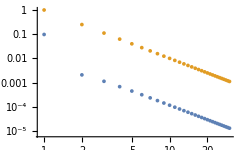

```mathematica
ListLogLogPlot[{Table[Abs[Re[fhat[k]]]/. n-> 10 /. g2 -> 1 /.g1-> 1 /. x-> 0.12 //N,{k,1,30}],Table[1/k^2,{k,1,30}]}]
```

```mathematica
(*Even with the taking absolute values with the imaginary component it remains quadratic.*)
```

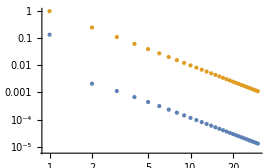

```mathematica
ListLogLogPlot[{Table[Abs[fhat[k]]/. n-> 10 /. g2 -> 1 /.g1-> 1 /. x-> 0.12 //N,{k,1,30}],Table[1/k^2,{k,1,30}]}]
```

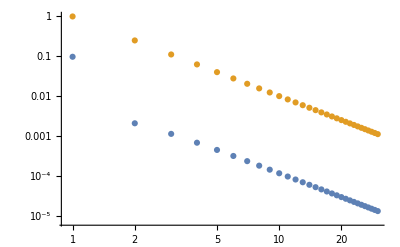

```mathematica
ListLogLogPlot[{Table[Abs[Re[fhatsimp[k]]]/. n-> 10 /. g2 -> 1 /.g1-> 1 /. x-> 0.12 //N,{k,1,30}],Table[1/k^2,{k,1,30}]}]
```

```mathematica
(*As we increase n, the FT tail decays still like quadratically. However as n increases, the absolute error increases, i.e. Subscript[C, n,x]h^2. Subscript[C, n,x]should grow like n, but |∫Subscript[C, n,x]|<const. *)
```

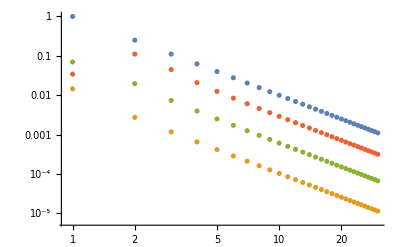

```mathematica
ListLogLogPlot[{Table[1/k^2,{k,1,30}],
Table[Abs[Re[fhat[k]]] /. g2 -> 1 /.n->3/.g1-> 1 /. x-> 0.9 //N,{k,1,30}],Table[Abs[Re[fhat[k]]] /. g2 -> 1 /.n->10/.g1-> 1 /. x-> 0.9 //N,{k,1,30}],
Table[Abs[Re[fhat[k]]] /. g2 -> 1 /.n->30/.g1-> 1 /. x-> 0.9 //N,{k,1,30}]}]
```

```mathematica
Assuming[n>0 &&g1>0 &&g2>0 && Element[g1, Reals] && Element[g2, Reals]&& Element[x, Reals]&& Element[y, Reals] && Element[n, Reals],FourierCosTransform[f[t],t,s,FourierParameters->{0,-2Pi}]]
```

1/2 ⅇ^(-(4 π s (π s+ⅈ n x))/n-2 g1 (g2 n+2 ⅈ π s+n x)) (-ⅇ^(2 (g1^2 n+(π^2 s^2)/n+g2 n x+3 ⅈ π s x)) Erf[(2 g1 n-2 ⅈ π s-n x)/(√2 √n)]+ⅇ^(2 (g1^2 n+(π^2 s^2)/n+g2 n x+3 ⅈ π s x)) Erf[(2 g1 n-g2 n-2 ⅈ π s-n x)/(√2 √n)]+ⅇ^((2 π s (π s+3 ⅈ n x))/n+2 g1 (g2 n+2 ⅈ π s+n x)) Erf[(g2 n-2 ⅈ π s-n x)/(√2 √n)]-ⅇ^(2 (g1^2 n+4 ⅈ g1 π s+g2 n x+(π s (π s+ⅈ n x))/n)) Erf[(2 g1 n+2 ⅈ π s-n x)/(√2 √n)]+ⅇ^(2 (g1^2 n+4 ⅈ g1 π s+g2 n x+(π s (π s+ⅈ n x))/n)) Erf[(2 g1 n-g2 n+2 ⅈ π s-n x)/(√2 √n)]+ⅇ^((2 π s (π s+ⅈ n x))/n+2 g1 (g2 n+2 ⅈ π s+n x)) Erf[(g2 n+2 ⅈ π s-n x)/(√2 √n)]+ⅈ ⅇ^((2 π s (π s+3 ⅈ n x))/n+2 g1 (g2 n+2 ⅈ π s+n x)) Erfi[(2 π s-ⅈ n x)/(√2 √n)]-ⅈ ⅇ^((2 π s (π s+ⅈ n x))/n+2 g1 (g2 n+2 ⅈ π s+n x)) Erfi[(2 π s+ⅈ n x)/(√2 √n)])

```mathematica
fhatcos[s_]:=1/2 ⅇ^(-(4 π s (π s+ⅈ n x))/n-2 g1 (g2 n+2 ⅈ π s+n x)) (-ⅇ^(2 (g1^2 n+(π^2 s^2)/n+g2 n x+3 ⅈ π s x)) Erf[(2 g1 n-2 ⅈ π s-n x)/(√2 √n)]+ⅇ^(2 (g1^2 n+(π^2 s^2)/n+g2 n x+3 ⅈ π s x)) Erf[(2 g1 n-g2 n-2 ⅈ π s-n x)/(√2 √n)]+ⅇ^((2 π s (π s+3 ⅈ n x))/n+2 g1 (g2 n+2 ⅈ π s+n x)) Erf[(g2 n-2 ⅈ π s-n x)/(√2 √n)]-ⅇ^(2 (g1^2 n+4 ⅈ g1 π s+g2 n x+(π s (π s+ⅈ n x))/n)) Erf[(2 g1 n+2 ⅈ π s-n x)/(√2 √n)]+ⅇ^(2 (g1^2 n+4 ⅈ g1 π s+g2 n x+(π s (π s+ⅈ n x))/n)) Erf[(2 g1 n-g2 n+2 ⅈ π s-n x)/(√2 √n)]+ⅇ^((2 π s (π s+ⅈ n x))/n+2 g1 (g2 n+2 ⅈ π s+n x)) Erf[(g2 n+2 ⅈ π s-n x)/(√2 √n)]+ⅈ ⅇ^((2 π s (π s+3 ⅈ n x))/n+2 g1 (g2 n+2 ⅈ π s+n x)) Erfi[(2 π s-ⅈ n x)/(√2 √n)]-ⅈ ⅇ^((2 π s (π s+ⅈ n x))/n+2 g1 (g2 n+2 ⅈ π s+n x)) Erfi[(2 π s+ⅈ n x)/(√2 √n)])
```

```mathematica
fhat[-15]/. n-> 10 /. g2 -> 1 /.g1-> 1 /. x-> 0 //N
```

-0.0000189888-2.11758×10^-19 ⅈ

```mathematica
fhat[15]/. n-> 10 /. g2 -> 1 /.g1-> 1 /. x-> 0 //N
```

-0.0000189888+2.11758×10^-19 ⅈ

```mathematica
fhatcos[-15]/. n-> 10 /. g2 -> 1 /.g1-> 1 /. x-> 0 //N
```

-0.0000379776-4.09375×10^-19 ⅈ

```mathematica
fhatcos[15]/. n-> 10 /. g2 -> 1 /.g1-> 1 /. x-> 0 //N
```

-0.0000379776+4.09375×10^-19 ⅈ

```mathematica
(*For the middle terms*)
```

```mathematica
f2[x1_]:=(1-Exp[-2n(g2-x2)(g1-x1)])PDF[NormalDistribution[0,1/(√n)],x2-x1](1-Exp[-2n(g0-x0)(g1-x1)])PDF[NormalDistribution[0,1/(√n)],x1-x0]If[x1<g1,1,0]
```

```mathematica
Assuming[n>0 &&g0>0&&g1>0 && g2>0 && Element[g0, Reals]&& Element[g1, Reals] && Element[g2, Reals]&& Element[x2, Reals]&& Element[x1, Reals]&& Element[x0, Reals] && Element[n, Reals],FourierTransform[f2[t],t,s,FourierParameters->{0,-2Pi}]]
```

(ⅇ^(-2 ⅈ g0 π s-2 ⅈ g2 π s-(π^2 s^2)/n-g0 n x0-g2 n x0-ⅈ π s x0+(n x0^2)/4-g0 n x2-g2 n x2-ⅈ π s x2-(n x0 x2)/2+(n x2^2)/4-1/2 n (4 g0 g1+4 g1 g2+x0^2+x2^2)) (-ⅇ^(g0^2 n+2 g1 g2 n+2 ⅈ g2 π s+2 g1 n x0+g2 n x0+2 ⅈ π s x0+2 g0 n x2+g2 n x2) n √((-2 g0+2 g1-2 g2+(2 ⅈ π s)/n+x0+x2)^2) √((2 g1 n+2 ⅈ π s-n x0-n x2)^2) √((2 g0 n-2 g1 n-2 ⅈ π s-n x0+n x2)^2) √((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2)-ⅇ^(2 g0 g1 n+g2^2 n+2 ⅈ g0 π s+g0 n x0+2 g2 n x0+g0 n x2+2 g1 n x2+2 ⅈ π s x2) n √((-2 g0+2 g1-2 g2+(2 ⅈ π s)/n+x0+x2)^2) √((2 g1 n+2 ⅈ π s-n x0-n x2)^2) √((2 g0 n-2 g1 n-2 ⅈ π s-n x0+n x2)^2) √((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2)+ⅇ^(2 g0 g1 n+2 g1 g2 n+2 ⅈ g0 π s+2 ⅈ g2 π s+g0 n x0+g2 n x0+g0 n x2+g2 n x2+n x0 x2) n √((-2 g0+2 g1-2 g2+(2 ⅈ π s)/n+x0+x2)^2) √((2 g1 n+2 ⅈ π s-n x0-n x2)^2) √((2 g0 n-2 g1 n-2 ⅈ π s-n x0+n x2)^2) √((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2)+ⅇ^(g0^2 n+2 g0 g2 n+g2^2 n+2 g1 n x0+2 ⅈ π s x0+2 g1 n x2+2 ⅈ π s x2+n x0 x2) n √((-2 g0+2 g1-2 g2+(2 ⅈ π s)/n+x0+x2)^2) √((2 g1 n+2 ⅈ π s-n x0-n x2)^2) √((2 g0 n-2 g1 n-2 ⅈ π s-n x0+n x2)^2) √((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2)+2 ⅇ^(g0^2 n+2 g1 g2 n+2 ⅈ g2 π s+2 g1 n x0+g2 n x0+2 ⅈ π s x0+2 g0 n x2+g2 n x2) g0 n^2 √((-2 g0+2 g1-2 g2+(2 ⅈ π s)/n+x0+x2)^2) √((2 g1 n+2 ⅈ π s-n x0-n x2)^2) √((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2) Erf[(√((-2 g0 n+2 g1 n+2 ⅈ π s+n x0-n x2)^2))/(2 √n)]-2 ⅇ^(g0^2 n+2 g1 g2 n+2 ⅈ g2 π s+2 g1 n x0+g2 n x0+2 ⅈ π s x0+2 g0 n x2+g2 n x2) g1 n^2 √((-2 g0+2 g1-2 g2+(2 ⅈ π s)/n+x0+x2)^2) √((2 g1 n+2 ⅈ π s-n x0-n x2)^2) √((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2) Erf[(√((-2 g0 n+2 g1 n+2 ⅈ π s+n x0-n x2)^2))/(2 √n)]-2 ⅈ ⅇ^(g0^2 n+2 g1 g2 n+2 ⅈ g2 π s+2 g1 n x0+g2 n x0+2 ⅈ π s x0+2 g0 n x2+g2 n x2) n π s √((-2 g0+2 g1-2 g2+(2 ⅈ π s)/n+x0+x2)^2) √((2 g1 n+2 ⅈ π s-n x0-n x2)^2) √((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2) Erf[(√((-2 g0 n+2 g1 n+2 ⅈ π s+n x0-n x2)^2))/(2 √n)]-ⅇ^(g0^2 n+2 g1 g2 n+2 ⅈ g2 π s+2 g1 n x0+g2 n x0+2 ⅈ π s x0+2 g0 n x2+g2 n x2) n^2 x0 √((-2 g0+2 g1-2 g2+(2 ⅈ π s)/n+x0+x2)^2) √((2 g1 n+2 ⅈ π s-n x0-n x2)^2) √((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2) Erf[(√((-2 g0 n+2 g1 n+2 ⅈ π s+n x0-n x2)^2))/(2 √n)]+ⅇ^(g0^2 n+2 g1 g2 n+2 ⅈ g2 π s+2 g1 n x0+g2 n x0+2 ⅈ π s x0+2 g0 n x2+g2 n x2) n^2 x2 √((-2 g0+2 g1-2 g2+(2 ⅈ π s)/n+x0+x2)^2) √((2 g1 n+2 ⅈ π s-n x0-n x2)^2) √((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2) Erf[(√((-2 g0 n+2 g1 n+2 ⅈ π s+n x0-n x2)^2))/(2 √n)]-2 ⅇ^(2 g0 g1 n+g2^2 n+2 ⅈ g0 π s+g0 n x0+2 g2 n x0+g0 n x2+2 g1 n x2+2 ⅈ π s x2) g1 n^2 √((-2 g0+2 g1-2 g2+(2 ⅈ π s)/n+x0+x2)^2) √((2 g1 n+2 ⅈ π s-n x0-n x2)^2) √((2 g0 n-2 g1 n-2 ⅈ π s-n x0+n x2)^2) Erf[(√((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2))/(2 √n)]+2 ⅇ^(2 g0 g1 n+g2^2 n+2 ⅈ g0 π s+g0 n x0+2 g2 n x0+g0 n x2+2 g1 n x2+2 ⅈ π s x2) g2 n^2 √((-2 g0+2 g1-2 g2+(2 ⅈ π s)/n+x0+x2)^2) √((2 g1 n+2 ⅈ π s-n x0-n x2)^2) √((2 g0 n-2 g1 n-2 ⅈ π s-n x0+n x2)^2) Erf[(√((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2))/(2 √n)]-2 ⅈ ⅇ^(2 g0 g1 n+g2^2 n+2 ⅈ g0 π s+g0 n x0+2 g2 n x0+g0 n x2+2 g1 n x2+2 ⅈ π s x2) n π s √((-2 g0+2 g1-2 g2+(2 ⅈ π s)/n+x0+x2)^2) √((2 g1 n+2 ⅈ π s-n x0-n x2)^2) √((2 g0 n-2 g1 n-2 ⅈ π s-n x0+n x2)^2) Erf[(√((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2))/(2 √n)]+ⅇ^(2 g0 g1 n+g2^2 n+2 ⅈ g0 π s+g0 n x0+2 g2 n x0+g0 n x2+2 g1 n x2+2 ⅈ π s x2) n^2 x0 √((-2 g0+2 g1-2 g2+(2 ⅈ π s)/n+x0+x2)^2) √((2 g1 n+2 ⅈ π s-n x0-n x2)^2) √((2 g0 n-2 g1 n-2 ⅈ π s-n x0+n x2)^2) Erf[(√((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2))/(2 √n)]-ⅇ^(2 g0 g1 n+g2^2 n+2 ⅈ g0 π s+g0 n x0+2 g2 n x0+g0 n x2+2 g1 n x2+2 ⅈ π s x2) n^2 x2 √((-2 g0+2 g1-2 g2+(2 ⅈ π s)/n+x0+x2)^2) √((2 g1 n+2 ⅈ π s-n x0-n x2)^2) √((2 g0 n-2 g1 n-2 ⅈ π s-n x0+n x2)^2) Erf[(√((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2))/(2 √n)]-2 ⅇ^(g0^2 n+2 g0 g2 n+g2^2 n+2 g1 n x0+2 ⅈ π s x0+2 g1 n x2+2 ⅈ π s x2+n x0 x2) g0 n √((2 g1 n+2 ⅈ π s-n x0-n x2)^2) √((2 g0 n-2 g1 n-2 ⅈ π s-n x0+n x2)^2) √((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2) Erf[(√((-2 g0 n+2 g1 n-2 g2 n+2 ⅈ π s+n x0+n x2)^2))/(2 √n)]+2 ⅇ^(g0^2 n+2 g0 g2 n+g2^2 n+2 g1 n x0+2 ⅈ π s x0+2 g1 n x2+2 ⅈ π s x2+n x0 x2) g1 n √((2 g1 n+2 ⅈ π s-n x0-n x2)^2) √((2 g0 n-2 g1 n-2 ⅈ π s-n x0+n x2)^2) √((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2) Erf[(√((-2 g0 n+2 g1 n-2 g2 n+2 ⅈ π s+n x0+n x2)^2))/(2 √n)]-2 ⅇ^(g0^2 n+2 g0 g2 n+g2^2 n+2 g1 n x0+2 ⅈ π s x0+2 g1 n x2+2 ⅈ π s x2+n x0 x2) g2 n √((2 g1 n+2 ⅈ π s-n x0-n x2)^2) √((2 g0 n-2 g1 n-2 ⅈ π s-n x0+n x2)^2) √((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2) Erf[(√((-2 g0 n+2 g1 n-2 g2 n+2 ⅈ π s+n x0+n x2)^2))/(2 √n)]+2 ⅈ ⅇ^(g0^2 n+2 g0 g2 n+g2^2 n+2 g1 n x0+2 ⅈ π s x0+2 g1 n x2+2 ⅈ π s x2+n x0 x2) π s √((2 g1 n+2 ⅈ π s-n x0-n x2)^2) √((2 g0 n-2 g1 n-2 ⅈ π s-n x0+n x2)^2) √((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2) Erf[(√((-2 g0 n+2 g1 n-2 g2 n+2 ⅈ π s+n x0+n x2)^2))/(2 √n)]+ⅇ^(g0^2 n+2 g0 g2 n+g2^2 n+2 g1 n x0+2 ⅈ π s x0+2 g1 n x2+2 ⅈ π s x2+n x0 x2) n x0 √((2 g1 n+2 ⅈ π s-n x0-n x2)^2) √((2 g0 n-2 g1 n-2 ⅈ π s-n x0+n x2)^2) √((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2) Erf[(√((-2 g0 n+2 g1 n-2 g2 n+2 ⅈ π s+n x0+n x2)^2))/(2 √n)]+ⅇ^(g0^2 n+2 g0 g2 n+g2^2 n+2 g1 n x0+2 ⅈ π s x0+2 g1 n x2+2 ⅈ π s x2+n x0 x2) n x2 √((2 g1 n+2 ⅈ π s-n x0-n x2)^2) √((2 g0 n-2 g1 n-2 ⅈ π s-n x0+n x2)^2) √((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2) Erf[(√((-2 g0 n+2 g1 n-2 g2 n+2 ⅈ π s+n x0+n x2)^2))/(2 √n)]+2 ⅇ^(2 g0 g1 n+2 g1 g2 n+2 ⅈ g0 π s+2 ⅈ g2 π s+g0 n x0+g2 n x0+g0 n x2+g2 n x2+n x0 x2) g1 n^2 √((-2 g0+2 g1-2 g2+(2 ⅈ π s)/n+x0+x2)^2) √((2 g0 n-2 g1 n-2 ⅈ π s-n x0+n x2)^2) √((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2) Erf[(√((2 g1 n+2 ⅈ π s-n (x0+x2))^2))/(2 √n)]+2 ⅈ ⅇ^(2 g0 g1 n+2 g1 g2 n+2 ⅈ g0 π s+2 ⅈ g2 π s+g0 n x0+g2 n x0+g0 n x2+g2 n x2+n x0 x2) n π s √((-2 g0+2 g1-2 g2+(2 ⅈ π s)/n+x0+x2)^2) √((2 g0 n-2 g1 n-2 ⅈ π s-n x0+n x2)^2) √((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2) Erf[(√((2 g1 n+2 ⅈ π s-n (x0+x2))^2))/(2 √n)]-ⅇ^(2 g0 g1 n+2 g1 g2 n+2 ⅈ g0 π s+2 ⅈ g2 π s+g0 n x0+g2 n x0+g0 n x2+g2 n x2+n x0 x2) n^2 x0 √((-2 g0+2 g1-2 g2+(2 ⅈ π s)/n+x0+x2)^2) √((2 g0 n-2 g1 n-2 ⅈ π s-n x0+n x2)^2) √((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2) Erf[(√((2 g1 n+2 ⅈ π s-n (x0+x2))^2))/(2 √n)]-ⅇ^(2 g0 g1 n+2 g1 g2 n+2 ⅈ g0 π s+2 ⅈ g2 π s+g0 n x0+g2 n x0+g0 n x2+g2 n x2+n x0 x2) n^2 x2 √((-2 g0+2 g1-2 g2+(2 ⅈ π s)/n+x0+x2)^2) √((2 g0 n-2 g1 n-2 ⅈ π s-n x0+n x2)^2) √((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2) Erf[(√((2 g1 n+2 ⅈ π s-n (x0+x2))^2))/(2 √n)]))/(4 √n √π √((-2 g0+2 g1-2 g2+(2 ⅈ π s)/n+x0+x2)^2) √((2 g1 n+2 ⅈ π s-n x0-n x2)^2) √((2 g0 n-2 g1 n-2 ⅈ π s-n x0+n x2)^2) √((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2))

```mathematica
f2hat[s_]:=(ⅇ^(-2 ⅈ g0 π s-2 ⅈ g2 π s-(π^2 s^2)/n-g0 n x0-g2 n x0-ⅈ π s x0+(n x0^2)/4-g0 n x2-g2 n x2-ⅈ π s x2-(n x0 x2)/2+(n x2^2)/4-1/2 n (4 g0 g1+4 g1 g2+x0^2+x2^2)) (-ⅇ^(g0^2 n+2 g1 g2 n+2 ⅈ g2 π s+2 g1 n x0+g2 n x0+2 ⅈ π s x0+2 g0 n x2+g2 n x2) n √((-2 g0+2 g1-2 g2+(2 ⅈ π s)/n+x0+x2)^2) √((2 g1 n+2 ⅈ π s-n x0-n x2)^2) √((2 g0 n-2 g1 n-2 ⅈ π s-n x0+n x2)^2) √((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2)-ⅇ^(2 g0 g1 n+g2^2 n+2 ⅈ g0 π s+g0 n x0+2 g2 n x0+g0 n x2+2 g1 n x2+2 ⅈ π s x2) n √((-2 g0+2 g1-2 g2+(2 ⅈ π s)/n+x0+x2)^2) √((2 g1 n+2 ⅈ π s-n x0-n x2)^2) √((2 g0 n-2 g1 n-2 ⅈ π s-n x0+n x2)^2) √((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2)+ⅇ^(2 g0 g1 n+2 g1 g2 n+2 ⅈ g0 π s+2 ⅈ g2 π s+g0 n x0+g2 n x0+g0 n x2+g2 n x2+n x0 x2) n √((-2 g0+2 g1-2 g2+(2 ⅈ π s)/n+x0+x2)^2) √((2 g1 n+2 ⅈ π s-n x0-n x2)^2) √((2 g0 n-2 g1 n-2 ⅈ π s-n x0+n x2)^2) √((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2)+ⅇ^(g0^2 n+2 g0 g2 n+g2^2 n+2 g1 n x0+2 ⅈ π s x0+2 g1 n x2+2 ⅈ π s x2+n x0 x2) n √((-2 g0+2 g1-2 g2+(2 ⅈ π s)/n+x0+x2)^2) √((2 g1 n+2 ⅈ π s-n x0-n x2)^2) √((2 g0 n-2 g1 n-2 ⅈ π s-n x0+n x2)^2) √((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2)+2 ⅇ^(g0^2 n+2 g1 g2 n+2 ⅈ g2 π s+2 g1 n x0+g2 n x0+2 ⅈ π s x0+2 g0 n x2+g2 n x2) g0 n^2 √((-2 g0+2 g1-2 g2+(2 ⅈ π s)/n+x0+x2)^2) √((2 g1 n+2 ⅈ π s-n x0-n x2)^2) √((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2) Erf[(√((-2 g0 n+2 g1 n+2 ⅈ π s+n x0-n x2)^2))/(2 √n)]-2 ⅇ^(g0^2 n+2 g1 g2 n+2 ⅈ g2 π s+2 g1 n x0+g2 n x0+2 ⅈ π s x0+2 g0 n x2+g2 n x2) g1 n^2 √((-2 g0+2 g1-2 g2+(2 ⅈ π s)/n+x0+x2)^2) √((2 g1 n+2 ⅈ π s-n x0-n x2)^2) √((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2) Erf[(√((-2 g0 n+2 g1 n+2 ⅈ π s+n x0-n x2)^2))/(2 √n)]-2 ⅈ ⅇ^(g0^2 n+2 g1 g2 n+2 ⅈ g2 π s+2 g1 n x0+g2 n x0+2 ⅈ π s x0+2 g0 n x2+g2 n x2) n π s √((-2 g0+2 g1-2 g2+(2 ⅈ π s)/n+x0+x2)^2) √((2 g1 n+2 ⅈ π s-n x0-n x2)^2) √((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2) Erf[(√((-2 g0 n+2 g1 n+2 ⅈ π s+n x0-n x2)^2))/(2 √n)]-ⅇ^(g0^2 n+2 g1 g2 n+2 ⅈ g2 π s+2 g1 n x0+g2 n x0+2 ⅈ π s x0+2 g0 n x2+g2 n x2) n^2 x0 √((-2 g0+2 g1-2 g2+(2 ⅈ π s)/n+x0+x2)^2) √((2 g1 n+2 ⅈ π s-n x0-n x2)^2) √((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2) Erf[(√((-2 g0 n+2 g1 n+2 ⅈ π s+n x0-n x2)^2))/(2 √n)]+ⅇ^(g0^2 n+2 g1 g2 n+2 ⅈ g2 π s+2 g1 n x0+g2 n x0+2 ⅈ π s x0+2 g0 n x2+g2 n x2) n^2 x2 √((-2 g0+2 g1-2 g2+(2 ⅈ π s)/n+x0+x2)^2) √((2 g1 n+2 ⅈ π s-n x0-n x2)^2) √((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2) Erf[(√((-2 g0 n+2 g1 n+2 ⅈ π s+n x0-n x2)^2))/(2 √n)]-2 ⅇ^(2 g0 g1 n+g2^2 n+2 ⅈ g0 π s+g0 n x0+2 g2 n x0+g0 n x2+2 g1 n x2+2 ⅈ π s x2) g1 n^2 √((-2 g0+2 g1-2 g2+(2 ⅈ π s)/n+x0+x2)^2) √((2 g1 n+2 ⅈ π s-n x0-n x2)^2) √((2 g0 n-2 g1 n-2 ⅈ π s-n x0+n x2)^2) Erf[(√((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2))/(2 √n)]+2 ⅇ^(2 g0 g1 n+g2^2 n+2 ⅈ g0 π s+g0 n x0+2 g2 n x0+g0 n x2+2 g1 n x2+2 ⅈ π s x2) g2 n^2 √((-2 g0+2 g1-2 g2+(2 ⅈ π s)/n+x0+x2)^2) √((2 g1 n+2 ⅈ π s-n x0-n x2)^2) √((2 g0 n-2 g1 n-2 ⅈ π s-n x0+n x2)^2) Erf[(√((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2))/(2 √n)]-2 ⅈ ⅇ^(2 g0 g1 n+g2^2 n+2 ⅈ g0 π s+g0 n x0+2 g2 n x0+g0 n x2+2 g1 n x2+2 ⅈ π s x2) n π s √((-2 g0+2 g1-2 g2+(2 ⅈ π s)/n+x0+x2)^2) √((2 g1 n+2 ⅈ π s-n x0-n x2)^2) √((2 g0 n-2 g1 n-2 ⅈ π s-n x0+n x2)^2) Erf[(√((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2))/(2 √n)]+ⅇ^(2 g0 g1 n+g2^2 n+2 ⅈ g0 π s+g0 n x0+2 g2 n x0+g0 n x2+2 g1 n x2+2 ⅈ π s x2) n^2 x0 √((-2 g0+2 g1-2 g2+(2 ⅈ π s)/n+x0+x2)^2) √((2 g1 n+2 ⅈ π s-n x0-n x2)^2) √((2 g0 n-2 g1 n-2 ⅈ π s-n x0+n x2)^2) Erf[(√((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2))/(2 √n)]-ⅇ^(2 g0 g1 n+g2^2 n+2 ⅈ g0 π s+g0 n x0+2 g2 n x0+g0 n x2+2 g1 n x2+2 ⅈ π s x2) n^2 x2 √((-2 g0+2 g1-2 g2+(2 ⅈ π s)/n+x0+x2)^2) √((2 g1 n+2 ⅈ π s-n x0-n x2)^2) √((2 g0 n-2 g1 n-2 ⅈ π s-n x0+n x2)^2) Erf[(√((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2))/(2 √n)]-2 ⅇ^(g0^2 n+2 g0 g2 n+g2^2 n+2 g1 n x0+2 ⅈ π s x0+2 g1 n x2+2 ⅈ π s x2+n x0 x2) g0 n √((2 g1 n+2 ⅈ π s-n x0-n x2)^2) √((2 g0 n-2 g1 n-2 ⅈ π s-n x0+n x2)^2) √((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2) Erf[(√((-2 g0 n+2 g1 n-2 g2 n+2 ⅈ π s+n x0+n x2)^2))/(2 √n)]+2 ⅇ^(g0^2 n+2 g0 g2 n+g2^2 n+2 g1 n x0+2 ⅈ π s x0+2 g1 n x2+2 ⅈ π s x2+n x0 x2) g1 n √((2 g1 n+2 ⅈ π s-n x0-n x2)^2) √((2 g0 n-2 g1 n-2 ⅈ π s-n x0+n x2)^2) √((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2) Erf[(√((-2 g0 n+2 g1 n-2 g2 n+2 ⅈ π s+n x0+n x2)^2))/(2 √n)]-2 ⅇ^(g0^2 n+2 g0 g2 n+g2^2 n+2 g1 n x0+2 ⅈ π s x0+2 g1 n x2+2 ⅈ π s x2+n x0 x2) g2 n √((2 g1 n+2 ⅈ π s-n x0-n x2)^2) √((2 g0 n-2 g1 n-2 ⅈ π s-n x0+n x2)^2) √((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2) Erf[(√((-2 g0 n+2 g1 n-2 g2 n+2 ⅈ π s+n x0+n x2)^2))/(2 √n)]+2 ⅈ ⅇ^(g0^2 n+2 g0 g2 n+g2^2 n+2 g1 n x0+2 ⅈ π s x0+2 g1 n x2+2 ⅈ π s x2+n x0 x2) π s √((2 g1 n+2 ⅈ π s-n x0-n x2)^2) √((2 g0 n-2 g1 n-2 ⅈ π s-n x0+n x2)^2) √((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2) Erf[(√((-2 g0 n+2 g1 n-2 g2 n+2 ⅈ π s+n x0+n x2)^2))/(2 √n)]+ⅇ^(g0^2 n+2 g0 g2 n+g2^2 n+2 g1 n x0+2 ⅈ π s x0+2 g1 n x2+2 ⅈ π s x2+n x0 x2) n x0 √((2 g1 n+2 ⅈ π s-n x0-n x2)^2) √((2 g0 n-2 g1 n-2 ⅈ π s-n x0+n x2)^2) √((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2) Erf[(√((-2 g0 n+2 g1 n-2 g2 n+2 ⅈ π s+n x0+n x2)^2))/(2 √n)]+ⅇ^(g0^2 n+2 g0 g2 n+g2^2 n+2 g1 n x0+2 ⅈ π s x0+2 g1 n x2+2 ⅈ π s x2+n x0 x2) n x2 √((2 g1 n+2 ⅈ π s-n x0-n x2)^2) √((2 g0 n-2 g1 n-2 ⅈ π s-n x0+n x2)^2) √((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2) Erf[(√((-2 g0 n+2 g1 n-2 g2 n+2 ⅈ π s+n x0+n x2)^2))/(2 √n)]+2 ⅇ^(2 g0 g1 n+2 g1 g2 n+2 ⅈ g0 π s+2 ⅈ g2 π s+g0 n x0+g2 n x0+g0 n x2+g2 n x2+n x0 x2) g1 n^2 √((-2 g0+2 g1-2 g2+(2 ⅈ π s)/n+x0+x2)^2) √((2 g0 n-2 g1 n-2 ⅈ π s-n x0+n x2)^2) √((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2) Erf[(√((2 g1 n+2 ⅈ π s-n (x0+x2))^2))/(2 √n)]+2 ⅈ ⅇ^(2 g0 g1 n+2 g1 g2 n+2 ⅈ g0 π s+2 ⅈ g2 π s+g0 n x0+g2 n x0+g0 n x2+g2 n x2+n x0 x2) n π s √((-2 g0+2 g1-2 g2+(2 ⅈ π s)/n+x0+x2)^2) √((2 g0 n-2 g1 n-2 ⅈ π s-n x0+n x2)^2) √((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2) Erf[(√((2 g1 n+2 ⅈ π s-n (x0+x2))^2))/(2 √n)]-ⅇ^(2 g0 g1 n+2 g1 g2 n+2 ⅈ g0 π s+2 ⅈ g2 π s+g0 n x0+g2 n x0+g0 n x2+g2 n x2+n x0 x2) n^2 x0 √((-2 g0+2 g1-2 g2+(2 ⅈ π s)/n+x0+x2)^2) √((2 g0 n-2 g1 n-2 ⅈ π s-n x0+n x2)^2) √((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2) Erf[(√((2 g1 n+2 ⅈ π s-n (x0+x2))^2))/(2 √n)]-ⅇ^(2 g0 g1 n+2 g1 g2 n+2 ⅈ g0 π s+2 ⅈ g2 π s+g0 n x0+g2 n x0+g0 n x2+g2 n x2+n x0 x2) n^2 x2 √((-2 g0+2 g1-2 g2+(2 ⅈ π s)/n+x0+x2)^2) √((2 g0 n-2 g1 n-2 ⅈ π s-n x0+n x2)^2) √((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2) Erf[(√((2 g1 n+2 ⅈ π s-n (x0+x2))^2))/(2 √n)]))/(4 √n √π √((-2 g0+2 g1-2 g2+(2 ⅈ π s)/n+x0+x2)^2) √((2 g1 n+2 ⅈ π s-n x0-n x2)^2) √((2 g0 n-2 g1 n-2 ⅈ π s-n x0+n x2)^2) √((2 g1 n-2 g2 n+2 ⅈ π s-n x0+n x2)^2))
```

```mathematica
FullSimplify[f2hat[s],n>0 &&g0>0&&g1>0 && g2>0 && Element[g0, Reals]&& Element[g1, Reals] && Element[g2, Reals]&& Element[x2, Reals]&& Element[x1, Reals]&& Element[x0, Reals] && Element[n, Reals]]
```

$Aborted